Membrane approach

v1.0
2019-11-05

Modeling the membrane-membrane interactions at the 1-40 nm range that membranes start from then must converge to during fusion
Looking at this via pressure, P

Pro-tip: Mathematica notation for scientific notation is 3.14*^-15

## First pass: Maximal repulsion of tensionless, uncharged membranes

Since they're uncharged, we can neglect the electrostatics
Keeping them tensionless here lets us ignore the poorly characterized (ie no one has an equation for it) suppression of undulations by tension

Thus P_tot = P_hydration + P_undulation + P_vdw

```mathematica
a=4.28*^-21
```

4.28×10^-21

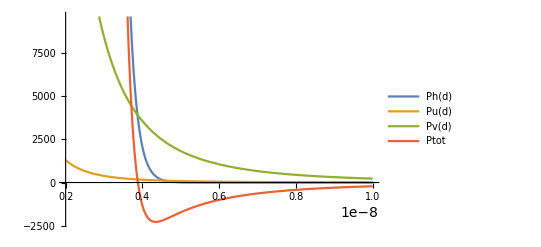

```mathematica
kT = 4.28*^-21; (*in J @ 37C*)
P0 = 1*^12; (*in Pa*)
c = 0.2*^-9; (*in m*)
B = 10*kT; (*in J*)
H = 1*kT;

Ph[d_]:=P0 * Exp[-d/c] (*Hydration repulsion*)
Pu[d_]:=(3*(kT^2))/(4*(Pi^3)*B*(d^3)) (*undulation pressure*)
Pv[d_]:=H/(6*Pi*(d^3)) (*van der Waals attraction*)

Ptot=Ph[d]+Pu[d]-Pv[d];
Plot[{Ph[d],Pu[d],Pv[d],Ptot},{d,2*^-9,10*^-9},PlotLegends->"Expressions"]
```

Great! We see a single clear point of equilibrium.  Note that P_vdw has been graphed as an absolute value.

OK, let' s get a feel for what this looks like at short range

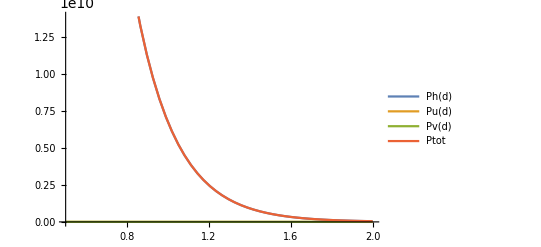

```mathematica
Plot[{Ph[d],Pu[d],Pv[d],Ptot},{d,0.5*^-9,2*^-9},PlotLegends->"Expressions"]
```

Let’s compare the above to our estimated maximum actin polymerization F from 2019-06-11 of ~70 nN for a 500 nm diameter cylinder
	That force on the given cylinder’s cap yields P = 3.565E5 Pa

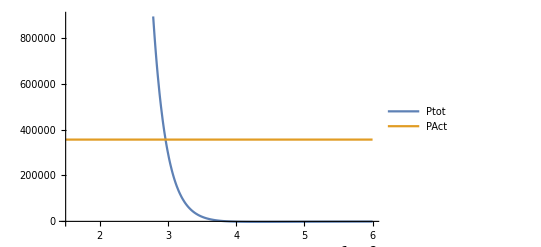

```mathematica
PAct=3.565*^5; (*in Pa*)
Plot[{Ptot,PAct},{d,1.5*^-9,6*^-9},PlotLegends->"Expressions"]
```